## Вычисление распада (B^0)_s->γ l^+l^- с учетом резонансных вкладов и с учетом кулоновского взаимодействия между лептонами в конечном состоянии.

## Часть 1. Константы, форм-факторы, Вильсоновские коэффициенты.

### 1) Массы.

Все величины указаны в МэВ.

```mathematica
MB = 5279.66;

MBs = 5366.3;

me = 0.511;

mmu = 105.658; 

mtau = 1776.86;

mb = 4850;

ms = 350.0;

mu = 230.0;

mc = 1450;
```

```mathematica
Γfull[type_]:=(6.58212 10^-16)/(1.519 10^-12 10^6)/; type=="Bgamma"
Γfull[type_]:=(6.58212 10^-16)/(1.520 10^-12 10^6)/; type=="Bsgamma"
```

### 2) Постоянная тонкой структуры, константа сильного взаимодействия и постоянная Ферми:

```mathematica
α = 1/137.04;

Gfermi = 1.166 10^-11;

αStr = 0.21;
```

Бегущая константа сильного взаимодействия взята на энергии 5 ГэВ из учебника Пескина и Шредера при нормировочном условии α_s(M_Z) = 0.117

### 3) Элементы матрицы Кабиббо-Кабаяши-Маскавы:

```mathematica
λ = 0.225;
ρ = 0.159;
A = 0.826;
η = 0.348;
```

```mathematica
Vud = 1-λ^2/2;
Vus = λ;
Vub = A λ^3(ρ-I η);

Vcd = -λ;
Vcs = 1-λ^2/2;
Vcb = A λ^2;
```

```mathematica
Vtb = 1;
Vts =-A λ^2;
Vtd = A λ^3(1-ρ-I η);
```

```mathematica
λu[supp_] := (Vub Vus*)/(Vtb Vts*)/; supp=="ts"
λu[supp_] := (Vub Vud*)/(Vtb Vtd*)/; supp=="td"
λc[supp_]:= (Vcb Vcs*)/(Vtb Vts*)/; supp=="ts"
λc[supp_]:= (Vcb Vcd*)/(Vtb Vtd*)/; supp=="td"
```

```mathematica
λu["ts"]+λc["ts"]+1
```

0.0172631+0.0176175 ⅈ

```mathematica
λu["td"]+λc["td"]+1
```

-0.00038547+0.0106336 ⅈ

### 4) Массы и ширины векторных резонансов:

Недостающие ширины взяты из рассчета распада V->l^+l^- на древесном уровне с гамильтонианом взаимодействия H^int(x) = g V^μ(x)l(x)γ_μ l(x) (только он дает удовлетворительные предсказания, ошибаясь не более чем на 10 %).

```mathematica
MJpsi = 3096.900;
ΓJpsi = 92.6 10^-3;
ΓJpsiEE = 0.05971 ΓJpsi; 
ΓJpsiMuMu = 0.05961 ΓJpsi; 
ΓJpsiTauTau = Re[Sqrt[(MJpsi^2 - 4 mtau^2)/(MJpsi^2 - 4 me^2)] (MJpsi^2 + 4 mtau^2)/(MJpsi^2 + 4 me^2)ΓJpsiEE]
```

0.

ψ(2S)-мезон:

```mathematica
MPsi2S = 3686.10;
ΓPsi2S = 0.294;
ΓPsi2SEE = 7.93 10^-3 ΓPsi2S;
ΓPsi2SMuMu = 8 10^-3 ΓPsi2S;
ΓPsi2STauTau = 3.1 10^-3 ΓPsi2S;
```

ψ(3770)-мезон:

```mathematica
MPsi3770 = 3773.7;
ΓPsi3770 = 0.0272;
ΓPsi3770EE = 9.6 10^-6 ΓPsi3770;
ΓPsi3770MuMu = Sqrt[(MPsi3770^2 - 4 mmu^2)/(MPsi3770^2 - 4 me^2)] (MPsi3770^2 + 4 mmu^2)/(MPsi3770^2 + 4 me^2) ΓPsi3770EE;
ΓPsi3770TauTau = Sqrt[(MPsi3770^2 - 4 mtau^2)/(MPsi3770^2 - 4 me^2)] (MPsi3770^2 + 4 mtau^2)/(MPsi3770^2 + 4 me^2)ΓPsi3770EE;
```

ψ(4040)-мезон:

```mathematica
MPsi4040 = 4039;
ΓPsi4040 = 0.08;
ΓPsi4040EE = 1.07 10^-5 ΓPsi4040;
ΓPsi4040MuMu = 9 10^-6 ΓPsi4040;
ΓPsi4040TauTau = Sqrt[(MPsi4040^2 - 4 mtau^2)/(MPsi4040^2 - 4 me^2)] (MPsi4040^2 + 4 mtau^2)/(MPsi4040^2 + 4 me^2)ΓPsi4040EE;
```

ψ(4160)-мезон:

```mathematica
MPsi4160 = 4191;
ΓPsi4160 = 0.07;
ΓPsi4160EE = 6.9 10^-6 ΓPsi4160;
ΓPsi4160MuMu = Sqrt[(MPsi4160^2 - 4 mmu^2)/(MPsi4160^2 - 4 me^2)] (MPsi4160^2 + 4 mmu^2)/(MPsi4160^2 + 4 me^2)ΓPsi4160EE;
ΓPsi4160TauTau = Sqrt[(MPsi4160^2 - 4 mtau^2)/(MPsi4160^2 - 4 me^2)] (MPsi4160^2 + 4 mtau^2)/(MPsi4160^2 + 4 me^2)ΓPsi4160EE;
```

ψ(4415)-мезон:

```mathematica
MPsi4415 = 4421;
ΓPsi4415 = 0.062;
ΓPsi4415EE = 9.4 10^-6 ΓPsi4415;
ΓPsi4415MuMu = 2 10^-5 ΓPsi4415;
ΓPsi4415TauTau = Sqrt[(MPsi4415^2 - 4 mtau^2)/(MPsi4415^2 - 4 me^2)] (MPsi4415^2 + 4 mtau^2)/(MPsi4415^2 + 4 me^2)ΓPsi4415EE;
```

ρ(770)-мезон:

```mathematica
Mrho770 = 775.26;
Γrho770 = 149.1;
Γrho770EE = 4.72 10^-5 Γrho770;
Γrho770MuMu = 4.55 10^-5 Γrho770;
Γrho770TauTau = Re[Sqrt[(Mrho770^2 - 4 mtau^2)/(Mrho770^2 - 4 me^2)] (Mrho770^2 + 4 mtau^2)/(Mrho770^2 + 4 me^2)Γrho770EE];
```

ω(782)-мезон:

```mathematica
Momega782 = 782.66;
ΓOmega782 = 8.49;
ΓOmega782EE = 7.38 10^-5 ΓOmega782;
ΓOmega782MuMu = 7.4 10^-5 ΓOmega782;
ΓOmega782TauTau = Re[Sqrt[(Momega782^2 - 4 mtau^2)/(Momega782^2 - 4 me^2)] (Momega782^2 + 4 mtau^2)/(Momega782^2 + 4 me^2)ΓOmega782EE];
```

ϕ(1019)-мезон: (в разделе с формфакторами)

### 5) Вспомогательные функции ω(s), h(m, s), h(0, s), H(m,s):

Эти функции необходимы для определения Вильсоновских коэффициентов с учетом резонансного вклада и вклада от c-анти-с петель. Определения взяты из работы [Описание четырехчастичных распадов Bd, s → µ+µ−e+e− в Стандартной Модели// А. В. Данилина Н. В. Никитин] и [Effective Hamiltonian for B  →  X_s e+ e- Beyond Leading Logarithms in the NDR and HV Schemes // A.J. Buras, M. Muenz]

Вспомогательная функция ω(s):

```mathematica
ω[s_] = -2/9 Pi^2 - 4/3 PolyLog[2,s] - 2/3 Log[s]Log[1-s]-(5+4 s)/(3(1+2s))Log[1-s] - (2s(1+s)(1-2s))/(3(1-s)^2(1+2s))Log[s]+(5+9s-6 s^2)/(6(1-s)(1+2s));
```

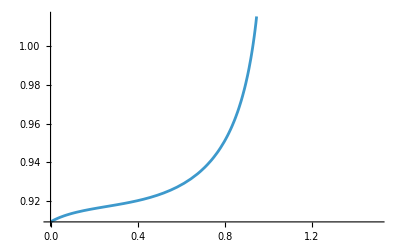

```mathematica
Plot[1+ αStr/Pi ω[s], {s, 0, 1.5}]
```

Вспомогательная функция h(m,s):

```mathematica
h[m_,s_] := -8/9 Log[m]+8/27+4/9(4 m^2)/s -2/9(2+(4 m^2)/s)Sqrt[Abs[1-(4 m^2)/s]] (Log[Abs[(Sqrt[1-(4 m^2)/s]+1)/(Sqrt[1-(4 m^2)/s]-1)]]-I Pi)/; (4 m^2)/s<=1 /; m!=0
h[m_,s_] := -8/9 Log[m]+8/27+4/9(4 m^2)/s -2/9(2+(4 m^2)/s)Sqrt[Abs[1-(4 m^2)/s]] 2 ArcTan[1/Sqrt[(4 m^2)/s - 1]]/; (4 m^2)/s>1 /; m!=0
h[m_,s_] :=8/27-4/9 Log[s] + 4/9 I Pi /; m==0
```

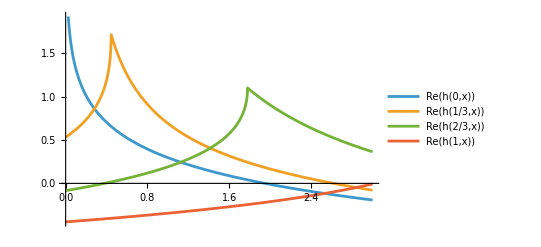

```mathematica
Plot[{Re[h[0,x]],  Re[h[1/3,x]], Re[h[2/3,x]], Re[h[1,x]]}, {x, 0, 3}, PlotLegends->"Expressions"]
```

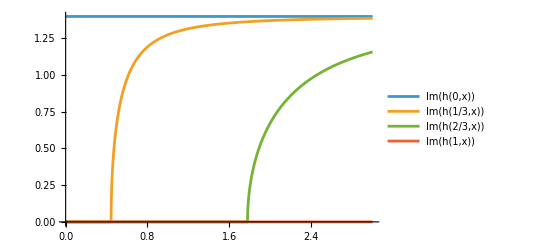

```mathematica
Plot[{Im[h[0,x]],  Im[h[1/3,x]], Im[h[2/3,x]], Im[h[1,x]]}, {x, 0, 3}, PlotLegends->"Expressions"]
```

Вспомогательная функция H(m_c,s):

```mathematica
Hc[m_,s_,lep_] := h[m,s]- (3 Pi)/α^2((mb^2 s)/MJpsi^2(MJpsi ΓJpsiEE)/(mb^2 s - MJpsi^2 + I MJpsi ΓJpsi) + (mb^2 s)/MPsi2S^2(MPsi2S ΓPsi2SEE)/(mb^2 s - MPsi2S^2 + I MPsi2S ΓPsi2S)+(mb^2 s)/MPsi3770^2(MPsi3770 ΓPsi3770EE)/(mb^2 s - MPsi3770^2 + I MPsi3770 ΓPsi3770)+(mb^2 s)/MPsi4040^2(MPsi4040 ΓPsi4040EE)/(mb^2 s - MPsi4040^2 + I MPsi4040 ΓPsi4040)+(mb^2 s)/MPsi4160^2(MPsi4160 ΓPsi4160EE)/(mb^2 s - MPsi4160^2 + I MPsi4160 ΓPsi4160)+(mb^2 s)/MPsi4415^2(MPsi4415 ΓPsi4415EE)/(mb^2 s - MPsi4415^2 + I MPsi4415 ΓPsi4415))/; lep=="e"
```

```mathematica
Hc[m_,s_,lep_] := h[m,s]- (3 Pi)/α^2((mb^2 s)/MJpsi^2(MJpsi ΓJpsiMuMu)/(mb^2 s - MJpsi^2 + I MJpsi ΓJpsi) + (mb^2 s)/MPsi2S^2(MPsi2S ΓPsi2SMuMu)/(mb^2 s - MPsi2S^2 + I MPsi2S ΓPsi2S)+(mb^2 s)/MPsi3770^2(MPsi3770 ΓPsi3770MuMu)/(mb^2 s - MPsi3770^2 + I MPsi3770 ΓPsi3770)+(mb^2 s)/MPsi4040^2(MPsi4040 ΓPsi4040MuMu)/(mb^2 s - MPsi4040^2 + I MPsi4040 ΓPsi4040)+(mb^2 s)/MPsi4160^2(MPsi4160 ΓPsi4160MuMu)/(mb^2 s - MPsi4160^2 + I MPsi4160 ΓPsi4160)+(mb^2 s)/MPsi4415^2(MPsi4415 ΓPsi4415MuMu)/(mb^2 s - MPsi4415^2 + I MPsi4415 ΓPsi4415))/; lep=="mu"
```

```mathematica
Hc[m_,s_,lep_] := h[m,s]- (3 Pi)/α^2((mb^2 s)/MJpsi^2(MJpsi ΓJpsiTauTau)/(mb^2 s - MJpsi^2 + I MJpsi ΓJpsi) + (mb^2 s)/MPsi2S^2(MPsi2S ΓPsi2STauTau)/(mb^2 s - MPsi2S^2 + I MPsi2S ΓPsi2S)+(mb^2 s)/MPsi3770^2(MPsi3770 ΓPsi3770TauTau)/(mb^2 s - MPsi3770^2 + I MPsi3770 ΓPsi3770)+(mb^2 s)/MPsi4040^2(MPsi4040 ΓPsi4040TauTau)/(mb^2 s - MPsi4040^2 + I MPsi4040 ΓPsi4040)+(mb^2 s)/MPsi4160^2(MPsi4160 ΓPsi4160TauTau)/(mb^2 s - MPsi4160^2 + I MPsi4160 ΓPsi4160)+(mb^2 s)/MPsi4415^2(MPsi4415 ΓPsi4415TauTau)/(mb^2 s - MPsi4415^2 + I MPsi4415 ΓPsi4415))/; lep=="tau"
```

```mathematica
LogPlot[Abs[Hc[1/4.58, MB^2/mb^2 x, "mu"]], {x, 0, 1.9}, PlotLabels->"|H(m_c=0,s)|",  Epilog->{Red,Table[InfiniteLine[{x,0},{0,1}],{x,{MJpsi^2/MB^2,MPsi2S^2/MB^2}}  ]  }]
```

-Graphics-

Вспомогательная функция H(m_u,s):

```mathematica
Hu[m_, s_, lep_] := h[m,s]-1/Sqrt[2](3 Pi)/α^2((mb^2 s)/Mrho770^2(Mrho770 Γrho770EE)/(mb^2 s - Mrho770^2 + I Mrho770 Γrho770) + (mb^2 s)/Momega782^2(Momega782 ΓOmega782EE)/(mb^2 s - Momega782^2 + I Momega782 ΓOmega782) )/; lep=="e"
```

```mathematica
Hu[m_, s_, lep_] := h[m,s]- 1/Sqrt[2](3 Pi)/α^2((mb^2 s)/Mrho770^2(Mrho770 Γrho770MuMu)/(mb^2 s - Mrho770^2 + I Mrho770 Γrho770) + (mb^2 s)/Momega782^2(Momega782 ΓOmega782MuMu)/(mb^2 s - Momega782^2 + I Momega782 ΓOmega782) )/; lep=="mu"
```

```mathematica
Hu[m_, s_, lep_] := h[m,s]- 1/Sqrt[2](3 Pi)/α^2((mb^2 s)/Mrho770^2(Mrho770 Γrho770TauTau)/(mb^2 s - Mrho770^2 + I Mrho770 Γrho770) + (mb^2 s)/Momega782^2(Momega782 ΓOmega782TauTau)/(mb^2 s - Momega782^2 + I Momega782 ΓOmega782) )/; lep=="tau"
```

```mathematica
Plot[Abs[Hu[0.5, x, "mu"]], {x, 0.02, 0.05}, PlotLabels->"|H(m_u=0,s)|"]
```

-Graphics-

### 6) Вильсоновские коэффициенты:

Подразумевается  соглашение C_2(M_W) = -1. Масштабный фактор, на котором берутся значения коэффициентов: μ_0 = 5 ГэВ.

 Численные значения взяты из работ, указывавшихся в пунтке (5) данного раздела.

```mathematica
C1 = 0.241;
C2 = -1.1;
C3 = -0.0104;
C4 = 0.02433;
C5= - 0.00706;
C6 = 0.0294;
C7gamma = 0.312;
C9V = -4.21;
C10A = 4.41;
```

Эффективный коэффициент Вильсона (C_(9V))^eff(μ, s), учитывающий с-анти-с петли, а также вклад резонансов:

```mathematica
C9Veff[s_,Mbmeson_, lep_,supp_] = (1+αStr/Pi ω[s mb^2/Mbmeson^2])C9V - (3C1+C2)(λu[supp] Hu[mu/mb,Mbmeson^2/mb^2 s,lep] + λc[supp] Hc[(1.3mc)/mb, Mbmeson^2/mb^2 s,lep])+(3 C3 + C4+ 3 C5+ C6) (2/9 + Hc[(1.3mc)/mb,Mbmeson^2/mb^2 s,lep])- 1/2(4C3 + 4C4 + 3C5+ C6) h[1, s] - 1/2(C3+ 3C4)h[ms/mb,s];
```

```mathematica
LogPlot[Abs[C9Veff[s, MB, "mu", "ts"]], {s, 0, 1.8},  PlotLabels->"|(C_(9  V))^eff(s)|",Epilog->{Red,Table[InfiniteLine[{x,0},{0,1}],{x,{MJpsi^2/MB^2,MPsi2S^2/MB^2}}  ]  }]
```

-Graphics-

```mathematica
Plot[Im[C9Veff[s, MB, "mu", "ts"]], {s, 0, 1.2},  PlotLabels->"Im((C_(9  V))^eff(s))"]
```

-Graphics-

```mathematica
Plot[Re[C9Veff[s, MB, "mu", "ts"]], {s, 0, 1.2},  PlotLabels->"Re((C_(9  V))^eff(s))"]
```

-Graphics-

### 7) Форм-факторы:

Определение форм-факторов и их численные значения взяты из работы [Rare FCNC radiative leptonic Bs;d → γl + l − decays in the standard model // Anastasiia Kozachuk, Dmitri Melikhov, and Nikolai Nikitin]

Константы f(0), σ_1, σ_2, M_R для распада B_d^0-> γ l^+l^-
1) Для функции F_A(q^2):

```mathematica
FAform0B = 0.072;
σFAB1 = 0.002;
σFAB2 = 0.400;
MRFAB = 5726;
```

2) Для функции F_V(q^2):

```mathematica
FVform0B = 0.110;
σFVB1 = 0.058;
σFVB2 = 0.489;
MRFVB = 5325;
```

3) Для функции F_TA(q^2):

```mathematica
FTAform0B = 0.117;
σFTAB1 = -0.091;
σFTAB2 = 0.180;
MRFTAB = 5726;
```

4) Для функции F_TV(q^2):

```mathematica
FTVform0B = 0.117;
σFTVB1 = 0.058;
σFTVB2 = 0.458;
MRFTVB = 5325;
```

Константы f(0), σ_1, σ_2, M_R для распада B_s^0-> γ l^+l^-
5) Для функции F_A(q^2):

```mathematica
FAform0Bs = 0.069;
σFABs1 = -0.031;
σFABs2 = 0.384;
MRFABs = 5829;
```

6) Для функции F_V(q^2):

```mathematica
FVform0Bs = 0.111;
σFVBs1 = 0.144;
σFVBs2 = 0.722;
MRFVBs = 5415;
```

7) Для функции F_TA(q^2):

```mathematica
FTAform0Bs = 0.119;
σFTABs1 = -0.063;
σFTABs2 = 0.321;
MRFTABs = 5829;
```

8) Для функции F_TV(q^2):

```mathematica
FTVform0Bs = 0.119;
σFTVBs1 = 0.163;
σFTVBs2 = 0.751;
MRFTVBs = 5415;
```

Формфакторы F_i(q^2,0):

```mathematica
error1[err_] := 1.10/; err=="+"
error1[err_] := 1.0/; err==""
error1[err_] := 0.9/; err=="-"
```

```mathematica
FA[s_, type_,err_] := (FAform0B error1[err])/((1-s MB^2/MRFAB^2)(1-σFAB1 s MB^2/MRFAB^2 + σFAB1 s^2 MB^4/MRFAB^4))/; type=="Bgamma"
FA[s_, type_,err_] := (FAform0Bs error1[err])/((1-s MBs^2/MRFABs^2)(1-σFABs1 s MBs^2/MRFABs^2 + σFABs1 s^2 MBs^4/MRFABs^4))/; type=="Bsgamma"
FV[s_, type_,err_] := (FVform0B error1[err])/((1-s MB^2/MRFVB^2)(1-σFVB1 s MB^2/MRFVB^2 + σFAB1 s^2 MB^4/MRFVB^4))/; type=="Bgamma"
FV[s_, type_,err_] := (FVform0Bs error1[err])/((1-s MBs^2/MRFVBs^2)(1-σFVBs1 s MBs^2/MRFVBs^2 + σFAB1 s^2 MBs^4/MRFVBs^4))/; type=="Bsgamma"
FTA[s_, type_,err_] := (FTAform0B error1[err])/((1-s MB^2/MRFTAB^2)(1-σFTAB1 s MB^2/MRFTAB^2 + σFTAB1 s^2 MB^4/MRFTAB^4))/; type=="Bgamma"
FTA[s_, type_,err_] := (FTAform0Bs error1[err])/((1-s MBs^2/MRFTABs^2)(1-σFTABs1 s MBs^2/MRFTABs^2 + σFTABs1 s^2 MBs^4/MRFTABs^4))/; type=="Bsgamma"
FTV[s_, type_,err_] := (FTVform0B error1[err])/((1-s MB^2/MRFTVB^2)(1-σFTVB1 s MB^2/MRFTVB^2 + σFTAB1 s^2 MB^4/MRFTVB^4))/; type=="Bgamma"
FTV[s_, type_,err_] := (FTVform0B error1[err])/((1-s MBs^2/MRFTVBs^2)(1-σFTVBs1 s MBs^2/MRFTVBs^2 + σFTAB1 s^2 MBs^4/MRFTVBs^4))/; type=="Bsgamma"
```

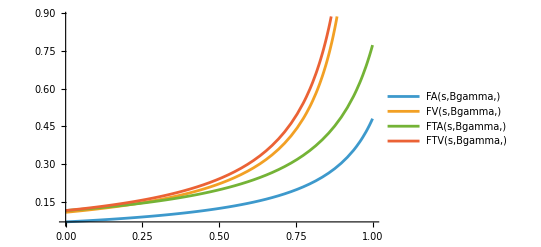

```mathematica
Plot[{FA[s, "Bgamma", ""],FV[s, "Bgamma", ""],FTA[s, "Bgamma", ""],FTV[s, "Bgamma", ""]},{s, 0, 1},PlotLegends->"Expressions"]
```

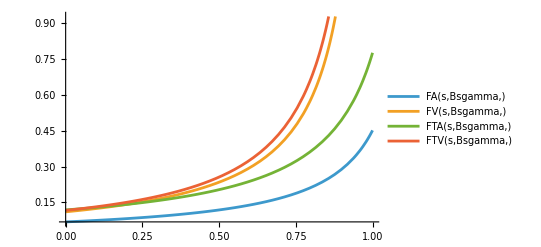

```mathematica
Plot[{FA[s, "Bsgamma", ""],FV[s, "Bsgamma", ""],FTA[s, "Bsgamma", ""],FTV[s, "Bsgamma", ""]},{s, 0, 1},PlotLegends->"Expressions"]
```

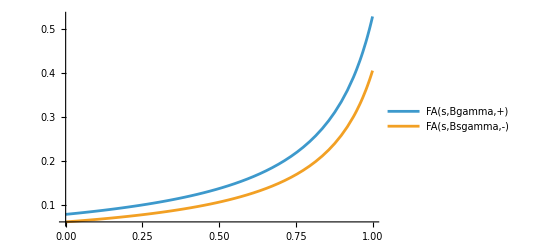

```mathematica
Plot[{FA[s, "Bgamma", "+"],FA[s, "Bsgamma", "-"]},{s, 0, 1},PlotLegends->"Expressions"]
```

Формфакторы F_i(0, q^2):

```mathematica
errorfrho[err_] := 1/; err=="+"
errorfrho[err_] := 0/; err==""
errorfrho[err_] := -1/; err=="-"
```

```mathematica
errorfomega[err_] := 4/; err=="+"
errorfomega[err_] := 0/; err==""
errorfomega[err_] := -4/; err=="-"

errorfphi[err_] := 5.5/; err=="+"
errorfphi[err_] := 0/; err==""
errorfphi[err_] := -5.5/; err=="-"

errorT1[err_] := 0.01/; err=="+"
errorT1[err_] := 0/; err==""
errorT1[err_] := -0.01/; err=="-"
```

```mathematica
frho = 221;
fomega = 191;
fphi = 220.5;
Mphi = 1019;
Γphi = 4.27;
T1Brho[err_] = -1/Sqrt[2](0.29+errorT1[err]);
T1Bomega [err_]= 1/Sqrt[2](0.24+errorT1[err]);
T1Bsphi[err_] = 0.27+errorT1[err];
frhoEM[err_] = 1/Sqrt[2](frho+errorfrho[err]);
fomegaEM[err_] = 1/(3Sqrt[2])(fomega+errorfomega[err]);
fphiEM[err_] = -1/3(fphi+errorfphi[err]);
```

Формфактор F_TA(0, q^2) := F_TA( q^2)' := (F_TA(q^2))_prime:

```mathematica
FTAprime[s_,type_,err_]:= FTAform0B error1[err]+ 2 frhoEM[err] T1Brho[err] (s MB^2/Mrho770)/(s MB^2 - Mrho770^2 + I Mrho770 Γrho770)+ 2 fomegaEM[err] T1Bomega[err] (s MB^2/Momega782)/(s MB^2 - Momega782^2 + I Momega782 ΓOmega782)/; type=="Bgamma"
FTAprime[s_,type_,err_]:= FTAform0Bs error1[err] + 2 fphiEM [err]T1Bsphi[err] (s MBs^2/Mphi)/(s MBs^2 - Mphi^2 + I Mphi Γphi)/; type=="Bsgamma"
FTVprime[s_,type_,err_]:= FTVform0B error1[err]+ 2 frhoEM [err]T1Brho [err](s MB^2/Mrho770)/(s MB^2 - Mrho770^2 + I Mrho770 Γrho770)+ 2 fomegaEM [err]T1Bomega[err] (s MB^2/Momega782)/(s MB^2 - Momega782^2 + I Momega782 ΓOmega782)/; type=="Bgamma"
FTVprime[s_,type_,err_]:= FTVform0Bs error1[err] + 2 fphiEM [err]T1Bsphi[err] (s MBs^2/Mphi)/(s MBs^2 - Mphi^2 + I Mphi Γphi)/; type=="Bsgamma"
```

```mathematica
FTAprime[0.4,"Bgamma","+"] - FTAprime[0.4,"Bgamma","-"]
```

0.0191707+0.0000730207 ⅈ

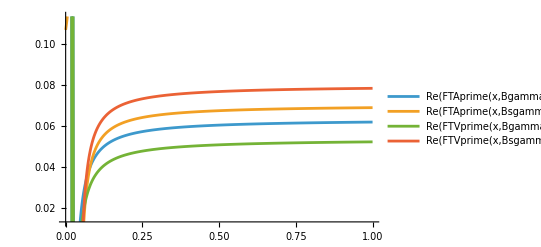

```mathematica
Plot[{Re[FTAprime[x,"Bgamma","+"]],Re[FTAprime[x,"Bsgamma","-"]],Re[FTVprime[x,"Bgamma",""]],Re[FTVprime[x,"Bsgamma",""]]}, {x, 0, 1}, PlotLegends->"Expressions"]
```

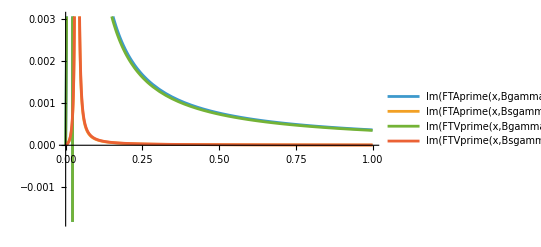

```mathematica
Plot[{Im[FTAprime[x,"Bgamma","+"]],Im[FTAprime[x,"Bsgamma","-"]],Im[FTVprime[x,"Bgamma",""]],Im[FTVprime[x,"Bsgamma",""]]}, {x, 0, 1}, PlotLegends->"Expressions"]
```

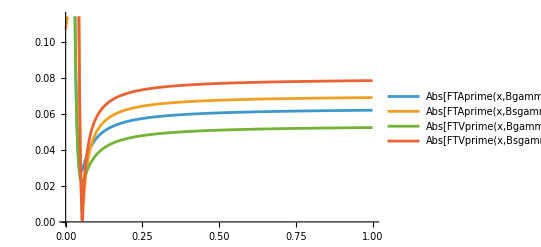

```mathematica
Plot[{Abs[FTAprime[x,"Bgamma","+"]],Abs[FTAprime[x,"Bsgamma","-"]],Abs[FTVprime[x,"Bgamma",""]],Abs[FTVprime[x,"Bsgamma",""]]}, {x, 0, 1}, PlotLegends->"Expressions"]
```

Формфактор (F^bar)_i(q^2)

```mathematica
a1 = -0.13;
errorfB[err_] := 4/; err=="+"
errorfB[err_] := 0/; err==""
errorfB[err_] := -4/; err=="-"
fB[type_,err_]:= 189+errorfB[err]/; type=="Bgamma"
fB[type_,err_]:= 225+errorfB[err]/; type=="Bsgamma"
Vuq[type_]:= Vud/; type=="Bgamma"
Vuq[type_]:= Vus/; type=="Bsgamma"
Vcq[type_]:= Vcd/; type=="Bgamma"
Vcq[type_]:= Vcs/; type=="Bsgamma"
Vtq[type_]:= Vtd/; type=="Bgamma"
Vtq[type_]:= Vts/; type=="Bsgamma"
```

```mathematica
FbarTA[s_, type_,err_] = FTA[s, type,err] +FTAprime[s, type,err];
FbarTV[s_, type_,err_] = FTV[s, type,err] +FTVprime[s, type,err] - 16/3(Vub Vuq[type]*+Vcb Vcq[type]*)/(Vtb Vtq[type]*)a1/C7gamma fB[type,err]/mb;
```

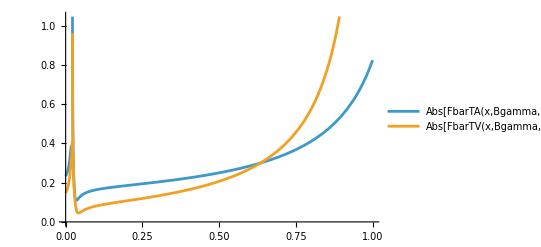

```mathematica
Plot[{Abs[FbarTA[x,"Bgamma",""]],Abs[FbarTV[x,"Bgamma",""]]}, {x, 0, 1}, PlotLegends->"Expressions"]
```

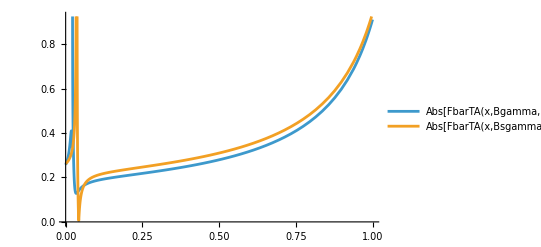

```mathematica
Plot[{Abs[FbarTA[x,"Bgamma","+"]],Abs[FbarTA[x,"Bsgamma","+"]]}, {x, 0, 1}, PlotLegends->"Expressions"]
```

## Часть 2. Дифференциальная ширина, branching ratio.

### 1) Вспомогательные функции F_1(q^2), F_2(q^2), B_0(q^2),B_1(q^2), B_2(q^2)

```mathematica
C9Vshort[s_,type_, lep_] := C9Veff[s,MB, lep,"td"]/; type=="Bgamma"
C9Vshort[s_,type_, lep_] := C9Veff[s,MBs, lep,"ts"]/; type=="Bsgamma"
mbhat[type_] := mb/MB/; type=="Bgamma"
mbhat[type_] := mb/MBs/; type=="Bsgamma"
mlhat[type_, lep_] := me/MB/; type=="Bgamma"/; lep=="e"
mlhat[type_, lep_] := mmu/MB/; type=="Bgamma"/; lep=="mu"
mlhat[type_, lep_] := mtau/MB/; type=="Bgamma"/; lep=="tau"
mlhat[type_, lep_] := me/MBs/; type=="Bsgamma"/; lep=="e"
mlhat[type_, lep_] := mmu/MBs/; type=="Bsgamma"/; lep=="mu"
mlhat[type_, lep_] := mtau/MBs/; type=="Bsgamma"/; lep=="tau"
```

```mathematica
F1[s_, type_, lep_, err_] = (Abs[C9Vshort[s,type, lep]]^2 + Abs[C10A]^2)FV[s, type, err]^2 + ((2mbhat[type])/s)^2 Abs[C7gamma FbarTV[s, type, err]]^2 + (4mbhat[type])/s FV[s, type, err]Re[C7gamma FbarTV[s, type, err] C9Vshort[s,type, lep]];
F2[s_, type_, lep_, err_] = (Abs[C9Vshort[s,type, lep]]^2 + Abs[C10A]^2)FA[s, type, err]^2 + ((2mbhat[type])/s)^2 Abs[C7gamma FbarTA[s, type, err]]^2 + (4mbhat[type])/s FA[s, type, err]Re[C7gamma FbarTA[s, type, err] C9Vshort[s,type, lep]];
B0[s_, type_, lep_, err_] = (s+4 mlhat[type, lep]^2)(F1[s,type, lep, err]+F2[s,type, lep, err]) - 8 mlhat[type,lep]^2 Abs[C10A]^2(FV[s, type, err]^2+FA[s, type, err]^2);
B1[s_, type_, lep_, err_] = 8(s FV[s, type, err]FA[s, type, err]Re[C9Vshort[s,type, lep]C10A] + mbhat[type] FV[s, type, err] Re[C7gamma*FbarTA[s, type, err]*C10A] + mbhat[type] FA[s, type, err] Re[C7gamma*FbarTV[s, type, err]*C10A]) ;
B2[s_, type_, lep_, err_] = s (F1[s,type, lep, err]+F2[s,type, lep, err]);
```

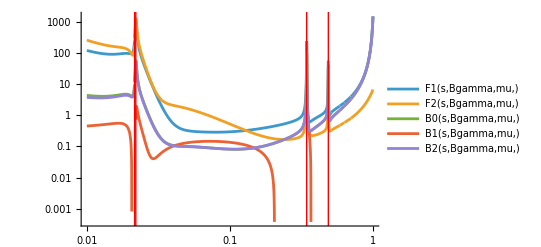

```mathematica
LogLogPlot[{F1[s,"Bgamma","mu", ""],F2[s,"Bgamma","mu", ""],B0[s,"Bgamma","mu", ""],B1[s,"Bgamma","mu", ""],B2[s,"Bgamma","mu", ""]},{s, 0.01, 1}, PlotLegends->"Expressions" ,Epilog->{Red,Table[InfiniteLine[{x,0},{0,1}],{x,{Log[Mrho770^2/MB^2],Log[Momega782^2/MB^2],Log[MJpsi^2/MB^2],Log[MPsi2S^2/MB^2]}}  ]  }]
```

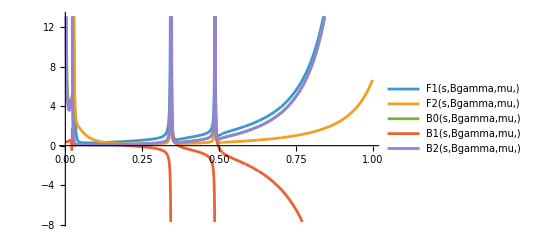

```mathematica
Plot[{F1[s,"Bgamma","mu", ""],F2[s,"Bgamma","mu", ""],B0[s,"Bgamma","mu", ""],B1[s,"Bgamma","mu", ""],B2[s,"Bgamma","mu", ""]},{s, 0.001, 1}, PlotLegends->"Expressions" ]
```

```mathematica
xhat[s_] =1-s;
uhat[s_,t_,type_, lep_] = 1 + 2 mlhat[type, lep]^2 -s-t;
ksi[s_,t_,type_, lep_] = uhat[s,t,type, lep] - t;
```

```mathematica
ϕ[s_] = 1 +s^2-2s;
tMand[s_,cos_,type_, lep_] = 1/2(1+2 mlhat[type, lep]^2 - s+Sqrt[ 1-4 mlhat[type, lep]^2/s]Sqrt[ϕ[s]]cos);
```

### 2) Дифференциальная ширина, определение функций.

```mathematica
Mb[type_] := MB/; type=="Bgamma"
Mb[type_] := MBs/; type=="Bsgamma"

dΓ1Free[s_,t_,type_, lep_,err_] =1/Γfull[type] (Gfermi^2 Mb[type]^5 α^3)/(2^10 Pi^4)Abs[Vtq[type]*Vtb]^2(xhat[s]^2 B0[s, type, lep,err] + xhat[s]ksi[s,t,type, lep]B1[s, type, lep,err] + ksi[s,t,type, lep]^2 B2[s, type, lep,err] );
dΓ2Free[s_,t_,type_, lep_,err_] = 1/Γfull[type] (Gfermi^2 Mb[type]^5 α^3)/(2^10 Pi^4)Abs[Vtq[type]*Vtb]^2((8fB[type,err])/Mb[type])^2 mlhat[type, lep]^2 Abs[C10A]^2((s+xhat[s]^2/2)/((uhat[s,t,type, lep] - mlhat[type, lep]^2)(t - mlhat[type, lep]^2)) - ((xhat[s]mlhat[type, lep])/((uhat[s,t,type, lep] - mlhat[type, lep]^2)(t - mlhat[type, lep]^2)))^2);
dΓ12Free[s_,t_,type_, lep_,err_] = - 1/Γfull[type] (Gfermi^2 Mb[type]^5 α^3)/(2^10 Pi^4)Abs[Vtq[type]*Vtb]^2(16fB[type,err])/Mb[type] mlhat[type, lep]^2(xhat[s]^2/((uhat[s,t,type, lep] - mlhat[type, lep]^2)(t - mlhat[type, lep]^2)))((2xhat[s]mbhat[type])/s Re[C10A*C7gamma FbarTV[s, type,err]] + xhat[s] FV[s,type,err] Re[C10A*C9Vshort[s,type, lep]] + ksi[s,t,type, lep]FA[s,type,err] Abs[C10A]^2);
dΓFree[s_,t_,type_, lep_,err_] = dΓ1Free[s,t,type, lep,err]+dΓ2Free[s,t,type, lep,err]+dΓ12Free[s,t,type, lep,err];
```

```mathematica
V[mRatio_] :=Sqrt[1 - 4 mRatio ] ;
```

```mathematica
Vrel[mRatio_] := V[mRatio]/(1 - 2 mRatio);
```

```mathematica
CAS[v_] := Abs[Gamma[Sqrt[1/4-α^2]+1/2+I α/v]/Gamma[Sqrt[1-4 α^2]+1]]^2 Exp[Pi α/v];
Furry[v_] := Exp[Pi α/v];
```

```mathematica
Ksoft[ΔE_,s_, type_, lep_]:=(2 ΔE/Mb[type])^((2 α/Pi)*(1/(4Vrel[mlhat[type, lep]^2/s]))*Log[(1+Vrel[mlhat[type, lep]^2/s])/(1-Vrel[mlhat[type, lep]^2/s])]);
```

```mathematica
Jacob[s_,type_, lep_] = 1/2 Sqrt[1 - (4 mlhat[type, lep]^2)/s]ϕ[s];
dΓAngleFree[s_,cos_,type_, lep_,err_] = dΓFree[s,tMand[s,cos,type, lep],type, lep,err]Jacob[s,type, lep];
dΓAngleCoulomb[s_,cos_,type_, lep_,err_] = dΓAngleFree[s,cos,type, lep,err]CAS[Vrel[mlhat[type, lep]^2/s]];
```

```mathematica
boundL[type_] := 0.02/; type=="Bgamma"
boundL[type_] := 0.025/; type=="Bsgamma"
boundR[type_] := 0.028/; type=="Bgamma"
boundR[type_] := 0.045/; type=="Bsgamma"
```

```mathematica
ClearAll[dΓAngleFreeCons]
```

```mathematica
dΓAngleFreeCons[s_,cos_,type_, lep_,err_] := dΓAngleFree[s,cos,type, lep,err]/; s<=boundL[type]/;MemberQ[{"e","mu"},lep]
dΓAngleFreeCons[s_,cos_,type_, lep_,err_] := 1/2(dΓAngleFree [boundL[type],cos, type, lep,err]+dΓAngleFree [boundR[type],cos, type, lep,err])/;s>=boundL[type]/;s<boundR[type]/;MemberQ[{"e","mu"},lep]
dΓAngleFreeCons[s_,cos_,type_, lep_,err_] := dΓAngleFree[s,cos,type, lep,err]/;s>=boundR[type]/;s<(Sqrt[8]1000)^2/Mb[type]^2/;MemberQ[{"e","mu"},lep]
dΓAngleFreeCons[s_,cos_,type_, lep_,err_] := 1/2(dΓAngleFree [(Sqrt[8]1000)^2/Mb[type]^2,cos, type, lep,err]+dΓAngleFree [(Sqrt[10]1000)^2/Mb[type]^2,cos, type, lep,err])/;s>=(Sqrt[8]1000)^2/Mb[type]^2/;s<(Sqrt[10]1000)^2/Mb[type]^2/;MemberQ[{"e","mu"},lep]
dΓAngleFreeCons[s_,cos_,type_, lep_,err_] := dΓAngleFree[s,cos,type, lep,err]/; s>=(Sqrt[10]1000)^2/Mb[type]^2/;s<(Sqrt[13]1000)^2/Mb[type]^2/;MemberQ[{"e","mu"},lep]
dΓAngleFreeCons[s_,cos_,type_, lep_,err_] := 1/2(dΓAngleFree [(Sqrt[13]1000)^2/Mb[type]^2,cos, type, lep,err]+dΓAngleFree [(Sqrt[14]1000)^2/Mb[type]^2,cos, type, lep,err])/;s>=(Sqrt[13]1000)^2/Mb[type]^2/;s<(Sqrt[14]1000)^2/Mb[type]^2/;MemberQ[{"e","mu"},lep]
dΓAngleFreeCons[s_,cos_,type_, lep_,err_] := dΓAngleFree[s,cos,type, lep,err]/; s>=(Sqrt[14]1000)^2/Mb[type]^2/;MemberQ[{"e","mu"},lep]


dΓAngleFreeCons[s_,cos_,type_, lep_,err_] :=dΓAngleFree[s,cos,type, lep,err]/; s<=(Sqrt[13]1000)^2/Mb[type]^2/;MemberQ[{"tau"},lep]
dΓAngleFreeCons[s_,cos_,type_, lep_,err_] :=1/2(dΓAngleFree[(Sqrt[13]1000)^2/Mb[type]^2,cos,type, lep,err]+dΓAngleFree[(Sqrt[14]1000)^2/Mb[type]^2,cos,type, lep,err])/;s>=(Sqrt[13]1000)^2/Mb[type]^2/;s<(Sqrt[14]1000)^2/Mb[type]^2/;MemberQ[{"tau"},lep]
dΓAngleFreeCons[s_,cos_,type_, lep_,err_] :=dΓAngleFree[s,cos,type, lep,err]/; s>=(Sqrt[14]1000)^2/Mb[type]^2/;MemberQ[{"tau"},lep]
dΓAngleCoulombCons[s_,cos_,type_, lep_,err_]  = dΓAngleFreeCons[s,cos,type, lep,err]CAS[Vrel[mlhat[type, lep]^2/s]];
```

```mathematica
dΓAngleFree [0.1, 0., "Bgamma", "mu",""]
```

9.99707×10^-12

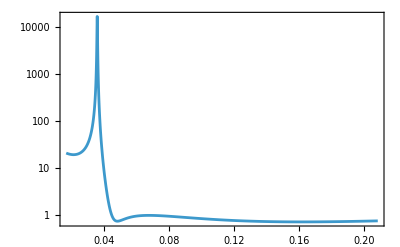

```mathematica
LogPlot[NIntegrate[10^9 dΓAngleFree [s, cos, "Bsgamma", "mu",""], {cos, -1, 1}], {s, (700/MBs)^2, ((Sqrt[6]1000)/MBs)^2}, PlotRange->All, GridLines->Automatic,Frame->True]
```

```mathematica
graphicsBgammaLL ={Plot3D[10^10 dΓAngleFree [s, cos, "Bgamma", "e",""], {s,4 mlhat["Bgamma", "e"]^2,1},{cos, -1, 1},ScalingFunctions->{Identity,Identity,"Log"},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^10 dΓAngleFree [s, cos, "Bgamma", "mu",""], {s,4 mlhat["Bgamma", "mu"]^2,1},{cos, -1, 1},ScalingFunctions->{Identity,Identity,"Log"},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50],Plot3D[10^10 dΓAngleFree [s, cos, "Bgamma", "tau",""], {s,4 mlhat["Bgamma", "tau"]^2,1},{cos, -1, 1},ScalingFunctions->{Identity,Identity,"Log"},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->50]}
```

$Aborted

```mathematica
graphicsBsgammaLL ={Plot3D[10^10 dΓAngleFree [s, cos, "Bsgamma", "e",""], {s,4 mlhat["Bsgamma", "e"]^2,1},{cos, -1, 1},ScalingFunctions->{Identity,Identity,"Log"},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->60],Plot3D[10^10 dΓAngleFree [s, cos, "Bsgamma", "mu",""], {s,4 mlhat["Bsgamma", "mu"]^2,1},{cos, -1, 1},ScalingFunctions->{Identity,Identity,"Log"},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->60],Plot3D[10^10 dΓAngleFree [s, cos, "Bsgamma", "tau",""], {s,4 mlhat["Bsgamma", "tau"]^2,1},{cos, -1, 1},ScalingFunctions->{Identity,Identity,"Log"},AxesLabel->{"s", "cos(θ)", "dΓ"},PlotPoints->60]}
```

$Aborted

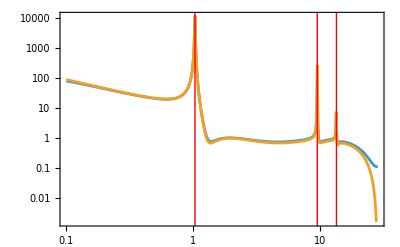

```mathematica
LogLogPlot[{NIntegrate[ 10^9 dΓAngleFree [(1000^2 s)/MBs^2, cos, "Bsgamma", "mu",""], {cos, -1, 1}],NIntegrate[ 10^9 dΓAngleFree [(1000^2 s)/MBs^2, cos, "Bsgamma", "e",""], {cos, -1, 1}]}, {s, 0.1, MBs^2/1000^2}, GridLines->Automatic,Frame->True,Epilog->{Red,Table[InfiniteLine[{x,0},{0,1}],{x,{Log[Mphi^2/1000^2],Log[MJpsi^2/1000^2],Log[MPsi2S^2/1000^2]}}  ]  }, PlotPoints->10  ]
```

```mathematica
LogplotsBgammaLL = {LogLogPlot[{NIntegrate[ 10^10 dΓAngleFree [(1000^2 s)/MB^2, cos, "Bgamma", "mu",""], {cos, -1, 1}],NIntegrate[ 10^10 dΓAngleFree [(1000^2 s)/MB^2, cos, "Bgamma", "e",""], {cos, -1, 1}]}, {s, 0.1, 20}, GridLines->Automatic,Frame->True,Epilog->{Red,Table[InfiniteLine[{x,0},{0,1}],{x,{Log[Mrho770^2/1000^2],Log[Momega782^2/1000^2],Log[MJpsi^2/1000^2],Log[MPsi2S^2/1000^2]}}  ]  }, PlotPoints->50  ],LogLogPlot[{NIntegrate[ 10^9 dΓAngleFree [(1000^2 s)/MBs^2, cos, "Bsgamma", "mu",""], {cos, -1, 1}],NIntegrate[ 10^9 dΓAngleFree [(1000^2 s)/MBs^2, cos, "Bsgamma", "e",""], {cos, -1, 1}]}, {s, 0.1, 20}, GridLines->Automatic,Frame->True,Epilog->{Red,Table[InfiniteLine[{x,0},{0,1}],{x,{Log[Mphi^2/1000^2],Log[MJpsi^2/1000^2],Log[MPsi2S^2/1000^2]}}  ]  }, PlotPoints->50  ]}
```

```mathematica
MPsi2S
```

3686.1

```mathematica
Export["BgammaEEMuMu.pdf",TableForm[LogplotsBgammaLL],ImageResolution->500,"CompressionLevel"->0]
```

BgammaEEMuMu.pdf

```mathematica
"BgammaEEMuMu.pdf"
```

BgammaEEMuMu.pdf

```mathematica
LogLogPlot[{NIntegrate[10^9 dΓAngleFreeCons [s, cos, "Bsgamma", "mu",""], {cos, -1, 1}],NIntegrate[10^9 dΓAngleFreeCons [s, cos, "Bsgamma", "e",""], {cos, -1, 1}]}, {s, 4 mlhat["Bgamma", "mu"]^2, 1.}, GridLines->Automatic,Frame->True,PlotLegends->{"Bs->gamma e e", "Bs->gamma mu mu"}]
```

```mathematica
Plot[Quiet[NIntegrate[10^10 dΓAngleFreeCons [s, cos, "Bgamma", "mu",""], {s, 4 mlhat["Bgamma", "mu"]^2, 1.}]], {cos, -1, 1}, GridLines->Automatic,Frame->True]
```

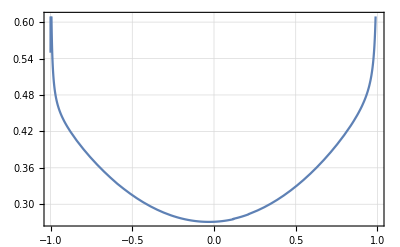
```mathematica
Export["BgammaMuMuangle.pdf",-Graphics-,ImageResolution->500,"CompressionLevel"->0]
```

BgammaMuMuangle.pdf

```mathematica
{(Sqrt[11]1000)^2/Mb["Bgamma"]^2,(Sqrt[12.5]1000)^2/Mb["Bgamma"]^2,(Sqrt[15]1000)^2/Mb["Bgamma"]^2}
```

{0.394622,0.448434,0.53812}

```mathematica
Plot[NIntegrate[10^10 dΓAngleFreeCons [s, cos, "Bsgamma", "tau",""], {cos, -1, 1}], {s, 4 mlhat["Bsgamma", "tau"]^2, 1.}, GridLines->Automatic,Frame->True]
```

```mathematica
Plot[NIntegrate[10^10 dΓAngleFreeCons [s, cos, "Bgamma", "tau",""], {cos, -1, 1}], {s, 4 mlhat["Bgamma", "tau"]^2, 1.}, GridLines->Automatic,Frame->True]
```

```mathematica
LogLogPlot[{NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "e","-"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "e","-"], {cos, -1, 1}],NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "e","+"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "e","+"], {cos, -1, 1}]}, {s, 4 mlhat["Bgamma", "mu"]^2, 1.},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}}, PlotStyle->{Black,Black,White,Black},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True]
```

```mathematica
Plot[{NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "e","-"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "e","-"], {cos, -1, 1}],NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "e","+"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "e","+"], {cos, -1, 1}]}, {s, 4 mlhat["Bgamma", "mu"]^2, 1.}, ScalingFunctions->{"Log",Identity},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}}, PlotStyle->{Black,Black,White,Black},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True]
```

```mathematica
Plot[{NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "tau","-"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "tau","-"], {cos, -1, 1}],NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "tau","+"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "tau","+"], {cos, -1, 1}]}, {s, 4 mlhat["Bgamma", "tau"]^2, 1.},Filling->{2->{{3},HatchFilling[(2.5Pi)/4, 5, 10]},1->{{2},Black}}, PlotStyle->{Black,Black,White,Black},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True]
```

### 3) Дифференциальная ширина, графики.

```mathematica
ClearAll[wthack]
wthack[clr_:Blue][{d___,h_HatchFilling}]:=PatternFilling[ColorReplace[Graphics[{d,h,Rectangle[]}],White->clr],ImageScaled[1]]
opac = 0.3;
clr = Black;
```

```mathematica
Plots ={ {Plot[{NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "e","-"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "e","-"], {cos, -1, 1}],NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "e","+"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "e","+"], {cos, -1, 1}]}, {s, 4 mlhat["Bgamma", "e"]^2, 1.},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "mu","-"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "mu","-"], {cos, -1, 1}],NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "mu","+"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "mu","+"], {cos, -1, 1}]}, {s, 4 mlhat["Bgamma", "mu"]^2, 0.999},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "tau","-"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "tau","-"], {cos, -1, 1}],NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "tau","+"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "tau","+"], {cos, -1, 1}]}, {s, 4 mlhat["Bgamma", "tau"]^2, 1.},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]},{Plot[{NIntegrate[10^10 dΓAngleFree [s, cos, "Bsgamma", "e","-"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bsgamma", "e","-"], {cos, -1, 1}],NIntegrate[10^10 dΓAngleFree [s, cos, "Bsgamma", "e","+"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bsgamma", "e","+"], {cos, -1, 1}]}, {s, 4 mlhat["Bsgamma", "e"]^2, 1.},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{NIntegrate[10^10 dΓAngleFree [s, cos, "Bsgamma", "mu","-"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bsgamma", "mu","-"], {cos, -1, 1}],NIntegrate[10^10 dΓAngleFree [s, cos, "Bsgamma", "mu","+"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bsgamma", "mu","+"], {cos, -1, 1}]}, {s, 4 mlhat["Bsgamma", "mu"]^2, 0.999},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{NIntegrate[10^10 dΓAngleFree [s, cos, "Bsgamma", "tau","-"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bsgamma", "tau","-"], {cos, -1, 1}],NIntegrate[10^10 dΓAngleFree [s, cos, "Bsgamma", "tau","+"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bsgamma", "tau","+"], {cos, -1, 1}]}, {s, 4 mlhat["Bsgamma", "tau"]^2, 1.},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]}}
```

```mathematica
Export["BgammaLLv5.pdf",TableForm[Plots],ImageResolution->500,"CompressionLevel"->0]
```

BgammaLLv3.pdf

```mathematica
Plot[{NIntegrate[10^10 dΓAngleFreeCons [s, cos, "Bgamma", "e","-"], {s, 4 mlhat["Bgamma", "e"]^2, 0.999}],NIntegrate[ 1.02 10^10 dΓAngleCoulombCons [s, cos, "Bgamma", "e","-"], {s, 4 mlhat["Bgamma", "e"]^2, 0.999}],NIntegrate[10^10 dΓAngleFreeCons [s, cos, "Bgamma", "e","+"], {s, 4 mlhat["Bgamma", "e"]^2, 0.999}],NIntegrate[ 1.02 10^10 dΓAngleCoulombCons [s, cos, "Bgamma", "e","+"], {s, 4 mlhat["Bgamma", "e"]^2, 0.999}]}, {cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]
```

```mathematica
Plot[{NIntegrate[10^10 dΓAngleFreeCons [s, cos, "Bgamma", "mu","-"], {s, 4 mlhat["Bgamma", "mu"]^2, 0.999}],NIntegrate[ 1.02 10^10 dΓAngleCoulombCons [s, cos, "Bgamma", "mu","-"], {s, 4 mlhat["Bgamma", "mu"]^2, 0.999}],NIntegrate[10^10 dΓAngleFreeCons [s, cos, "Bgamma", "mu","+"], {s, 4 mlhat["Bgamma", "mu"]^2, 0.999}],NIntegrate[ 1.02 10^10 dΓAngleCoulombCons [s, cos, "Bgamma", "mu","+"], {s, 4 mlhat["Bgamma", "mu"]^2, 0.999}]}, {cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]
```

```mathematica
Plot[{NIntegrate[10^10 dΓAngleFreeCons [s, cos, "Bgamma", "tau","-"], {s, 4 mlhat["Bgamma", "tau"]^2, 0.999}],NIntegrate[ 1.02 10^10 dΓAngleCoulombCons [s, cos, "Bgamma", "tau","-"], {s, 4 mlhat["Bgamma", "tau"]^2, 0.999}],NIntegrate[10^10 dΓAngleFreeCons [s, cos, "Bgamma", "tau","+"], {s, 4 mlhat["Bgamma", "tau"]^2, 0.999}],NIntegrate[ 1.02 10^10 dΓAngleCoulombCons [s, cos, "Bgamma", "tau","+"], {s, 4 mlhat["Bgamma", "tau"]^2, 0.999}]}, {cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]
```

```mathematica
Plot[{NIntegrate[10^10 dΓAngleFreeCons [s, cos, "Bsgamma", "e","-"], {s, 4 mlhat["Bsgamma", "e"]^2, 0.999}],NIntegrate[ 1.02 10^10 dΓAngleCoulombCons [s, cos, "Bsgamma", "e","-"], {s, 4 mlhat["Bsgamma", "e"]^2, 0.999}],NIntegrate[10^10 dΓAngleFreeCons [s, cos, "Bsgamma", "e","+"], {s, 4 mlhat["Bsgamma", "e"]^2, 0.999}],NIntegrate[ 1.02 10^10 dΓAngleCoulombCons [s, cos, "Bsgamma", "e","+"], {s, 4 mlhat["Bsgamma", "e"]^2, 0.999}]}, {cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]
```

```mathematica
Plot[{NIntegrate[10^10 dΓAngleFreeCons [s, cos, "Bsgamma", "mu","-"], {s, 4 mlhat["Bsgamma", "mu"]^2, 0.999}],NIntegrate[ 1.02 10^10 dΓAngleCoulombCons [s, cos, "Bsgamma", "mu","-"], {s, 4 mlhat["Bsgamma", "mu"]^2, 0.999}],NIntegrate[10^10 dΓAngleFreeCons [s, cos, "Bsgamma", "mu","+"], {s, 4 mlhat["Bsgamma", "mu"]^2, 0.999}],NIntegrate[ 1.02 10^10 dΓAngleCoulombCons [s, cos, "Bsgamma", "mu","+"], {s, 4 mlhat["Bsgamma", "mu"]^2, 0.999}]}, {cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.0461999}. NIntegrate obtained 13.632 and 0.0298624 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.0461999}. NIntegrate obtained 14.251 and 0.0261134 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.0461999}. NIntegrate obtained 18.1954 and 0.0437102 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Plot[{NIntegrate[10^10 dΓAngleFreeCons [s, cos, "Bsgamma", "tau","-"], {s, 4 mlhat["Bsgamma", "tau"]^2, 0.999}],NIntegrate[ 1.02 10^10 dΓAngleCoulombCons [s, cos, "Bsgamma", "tau","-"], {s, 4 mlhat["Bsgamma", "tau"]^2, 0.999}],NIntegrate[10^10 dΓAngleFreeCons [s, cos, "Bsgamma", "tau","+"], {s, 4 mlhat["Bsgamma", "tau"]^2, 0.999}],NIntegrate[ 1.02 10^10 dΓAngleCoulombCons [s, cos, "Bsgamma", "tau","+"], {s, 4 mlhat["Bsgamma", "tau"]^2, 0.999}]}, {cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.471890073617027}. NIntegrate obtained 1.70056 and 0.0505347 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.471890073617027}. NIntegrate obtained 1.83165 and 0.0561138 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.471890073617027}. NIntegrate obtained 2.05677 and 0.0753889 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

BgammaLLdcosv6.pdf

```mathematica
PlotsAngles ={ {Plot[{NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "e","-"], {s, 4 mlhat["Bgamma", "e"]^2, 1.}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "e","-"], {s, 4 mlhat["Bgamma", "e"]^2, 1.}],NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "e","+"], {s, 4 mlhat["Bgamma", "e"]^2, 1.}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "e","+"], {s, 4 mlhat["Bgamma", "e"]^2, 1.}]}, {cos, -1, 1},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "mu","-"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "mu","-"], {cos, -1, 1}],NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "mu","+"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "mu","+"], {cos, -1, 1}]}, {s, 4 mlhat["Bgamma", "mu"]^2, 0.999},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "tau","-"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "tau","-"], {cos, -1, 1}],NIntegrate[10^10 dΓAngleFree [s, cos, "Bgamma", "tau","+"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bgamma", "tau","+"], {cos, -1, 1}]}, {s, 4 mlhat["Bgamma", "tau"]^2, 1.},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]},{Plot[{NIntegrate[10^10 dΓAngleFree [s, cos, "Bsgamma", "e","-"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bsgamma", "e","-"], {cos, -1, 1}],NIntegrate[10^10 dΓAngleFree [s, cos, "Bsgamma", "e","+"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bsgamma", "e","+"], {cos, -1, 1}]}, {s, 4 mlhat["Bsgamma", "e"]^2, 1.},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{NIntegrate[10^10 dΓAngleFree [s, cos, "Bsgamma", "mu","-"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bsgamma", "mu","-"], {cos, -1, 1}],NIntegrate[10^10 dΓAngleFree [s, cos, "Bsgamma", "mu","+"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bsgamma", "mu","+"], {cos, -1, 1}]}, {s, 4 mlhat["Bsgamma", "mu"]^2, 0.999},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1],Plot[{NIntegrate[10^10 dΓAngleFree [s, cos, "Bsgamma", "tau","-"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bsgamma", "tau","-"], {cos, -1, 1}],NIntegrate[10^10 dΓAngleFree [s, cos, "Bsgamma", "tau","+"], {cos, -1, 1}],NIntegrate[ 1.02 10^10 dΓAngleCoulomb [s, cos, "Bsgamma", "tau","+"], {cos, -1, 1}]}, {s, 4 mlhat["Bsgamma", "tau"]^2, 1.},Filling->{4->{{3},Opacity[opac, clr]},3->{{2},wthack[Opacity[opac, clr]][{clr,HatchFilling[Pi/3,8,16]}]},1->{{2},clr}},PlotStyle->{clr,clr,Opacity[opac/50, clr],Opacity[opac/50, clr]},LabelStyle->{GrayLevel[0],Bold}, GridLines->Automatic,Frame->True,AspectRatio->1]}}
```

### 4) Branching ratio, расчеты.

{2.3467×10^-10,4.98434×10^-12}

```mathematica
IntegralsBgammaee = {Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bgamma", "e","-"],{s, (1000/MB)^2, ((Sqrt[6] 1000)/MB)^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bgamma", "e","+"],{s, (1000/MB)^2, ((Sqrt[6] 1000)/MB)^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "e","-"],{s, (1000/MB)^2, ((Sqrt[6] 1000)/MB)^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "e","+"],{s, (1000/MB)^2, ((Sqrt[6] 1000)/MB)^2}, {cos, -1, 1}]]};
ΓfreeBgammaee = {(IntegralsBgammaee[[1]]+IntegralsBgammaee[[2]])/2, (IntegralsBgammaee[[2]]-IntegralsBgammaee[[1]])/4,(IntegralsBgammaee[[3]]+IntegralsBgammaee[[4]])/2, (IntegralsBgammaee[[4]]-IntegralsBgammaee[[3]])/4, 100(IntegralsBgammaee[[3]]-IntegralsBgammaee[[1]])/IntegralsBgammaee[[1]]};
```

```mathematica
ΓfreeBgammaee
```

{5.09609×10^-12,5.92877×10^-13,5.2146×10^-12,6.06664×10^-13,2.32549}

```mathematica
IntegralsBgammamumu = {Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bgamma", "mu","-"],{s, (1000/MB)^2, ((Sqrt[6] 1000)/MB)^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bgamma", "mu","+"],{s, (1000/MB)^2, ((Sqrt[6] 1000)/MB)^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "mu","-"],{s, (1000/MB)^2, ((Sqrt[6] 1000)/MB)^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "mu","+"],{s, (1000/MB)^2, ((Sqrt[6] 1000)/MB)^2}, {cos, -1, 1}]]};
ΓfreeBgammamumu = {(IntegralsBgammamumu[[1]]+IntegralsBgammamumu[[2]])/2, (IntegralsBgammamumu[[2]]-IntegralsBgammamumu[[1]])/4,(IntegralsBgammamumu[[3]]+IntegralsBgammamumu[[4]])/2, (IntegralsBgammamumu[[4]]-IntegralsBgammamumu[[3]])/4, 100(IntegralsBgammamumu[[3]]-IntegralsBgammamumu[[1]])/IntegralsBgammamumu[[1]]};
```

```mathematica
IntegralsBgammatautau = {Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bgamma", "tau","-"],{ s, 4 mlhat["Bgamma", "tau"]^2, 1.}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bgamma", "tau","+"],{s,  4 mlhat["Bgamma", "tau"]^2, 1.}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "tau","-"],{s,  4 mlhat["Bgamma", "tau"]^2, 1.}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "tau","+"],{s,  4 mlhat["Bgamma", "tau"]^2, 1.}, {cos, -1, 1}]]};
ΓfreeBgammatautau  = {1/2(IntegralsBgammatautau[[1]]+IntegralsBgammatautau[[2]]), 1/4(IntegralsBgammatautau[[2]]-IntegralsBgammatautau[[1]]),1/2(IntegralsBgammatautau[[3]]+IntegralsBgammatautau[[4]]), 1/4(IntegralsBgammatautau[[4]]-IntegralsBgammatautau[[3]]), 100((IntegralsBgammatautau[[3]]-IntegralsBgammatautau[[1]])/IntegralsBgammatautau[[1]])};
```

```mathematica
ΓfreeBgammatautau
```

{3.36443×10^-11,1.1836×10^-12,3.514×10^-11,1.24659×10^-12,4.37935}

```mathematica
IntegralsBsgammaee = {Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bsgamma", "e","-"],{s, (1000/MBs)^2, ((Sqrt[6] 1000)/MBs)^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bsgamma", "e","+"],{s, (1000/MBs)^2, ((Sqrt[6] 1000)/MBs)^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bsgamma", "e","-"],{s, (1000/MBs)^2, ((Sqrt[6] 1000)/MBs)^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bsgamma", "e","+"],{s, (1000/MBs)^2, ((Sqrt[6] 1000)/MBs)^2}, {cos, -1, 1}]]};
ΓfreeBsgammaee = {(IntegralsBsgammaee[[1]]+IntegralsBsgammaee[[2]])/2, (IntegralsBsgammaee[[2]]-IntegralsBsgammaee[[1]])/4,(IntegralsBsgammaee[[3]]+IntegralsBsgammaee[[4]])/2, (IntegralsBsgammaee[[4]]-IntegralsBsgammaee[[3]])/4, 100(IntegralsBsgammaee[[3]]-IntegralsBsgammaee[[1]])/IntegralsBsgammaee[[1]]};
IntegralsBsgammamumu = {Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bsgamma", "mu","-"],{s, (1000/MBs)^2, ((Sqrt[6] 1000)/MBs)^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bsgamma", "mu","+"],{s, (1000/MBs)^2, ((Sqrt[6] 1000)/MBs)^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bsgamma", "mu","-"],{s, (1000/MBs)^2, ((Sqrt[6] 1000)/MBs)^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bsgamma", "mu","+"],{s, (1000/MBs)^2, ((Sqrt[6] 1000)/MBs)^2}, {cos, -1, 1}]]};
ΓfreeBsgammamumu = {1/2(IntegralsBsgammamumu[[1]]+IntegralsBsgammamumu[[2]]), 1/4(IntegralsBsgammamumu[[2]]-IntegralsBsgammamumu[[1]]),1/2(IntegralsBsgammamumu[[3]]+IntegralsBsgammamumu[[4]]), 1/4(IntegralsBsgammamumu[[4]]-IntegralsBsgammamumu[[3]]), 100((IntegralsBsgammamumu[[3]]-IntegralsBsgammamumu[[1]])/IntegralsBsgammamumu[[1]])};
```

```mathematica
IntegralsBsgammatautau = {Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bsgamma", "tau","-"],{s,  4 mlhat["Bsgamma", "tau"]^2, 1.}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bsgamma", "tau","+"],{s, 4 mlhat["Bsgamma", "tau"]^2, 1.}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bsgamma", "tau","-"],{s,4 mlhat["Bsgamma", "tau"]^2, 1.}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bsgamma", "tau","+"],{s, 4 mlhat["Bsgamma", "tau"]^2, 1.}, {cos, -1, 1}]]};
ΓfreeBsgammatautau  = {1/2(IntegralsBsgammatautau[[1]]+IntegralsBsgammatautau[[2]]), 1/4(IntegralsBsgammatautau[[2]]-IntegralsBsgammatautau[[1]]),1/2(IntegralsBsgammatautau[[3]]+IntegralsBsgammatautau[[4]]), 1/4(IntegralsBsgammatautau[[4]]-IntegralsBsgammatautau[[3]]), 100((IntegralsBsgammatautau[[3]]-IntegralsBsgammatautau[[1]])/IntegralsBsgammatautau[[1]])};
```

```mathematica
ΓfreeBsgammatautau
```

{1.13855×10^-9,3.00058×10^-11,1.16945×10^-9,3.08519×10^-11,2.70781}

```mathematica
ΓfreeBgammatautau
```

{3.10285×10^-11,9.2801×10^-13,3.18795×10^-11,9.54333×10^-13,2.73682}

```mathematica
4 mlhat["Bsgamma", "tau"]^2
```

0.438547

```mathematica
(1000/MBs)^2
```

0.0347256

```mathematica
((Sqrt[6] 1000)/MBs)^2
```

0.208354

```mathematica
Γall = {{ΓfreeBgammaee, ΓfreeBgammamumu,ΓfreeBgammatautau},{ΓfreeBsgammaee, ΓfreeBsgammamumu,ΓfreeBsgammatautau}};
```

```mathematica
MatrixForm[Γall]
```

((5.09609×10^-12
5.92877×10^-13
5.2146×10^-12
6.06664×10^-13
2.32549) | (5.31111×10^-12
5.75245×10^-13
5.43574×10^-12
5.88754×10^-13
2.34604) | (3.36443×10^-11
1.1836×10^-12
3.514×10^-11
1.24659×10^-12
4.37935)
(2.37698×10^-10
2.31739×10^-11
2.43226×10^-10
2.37128×10^-11
2.32549) | (2.472×10^-10
2.31584×10^-11
2.53026×10^-10
2.37043×10^-11
2.35663) | (1.19393×10^-9
3.54215×10^-11
1.24419×10^-9
3.71884×10^-11
4.16055))

```mathematica
(*2.2845087341867938*^-10*)




Quiet[NIntegrate[dΓAngleFree [s, cos, "Bsgamma", "e",""],{s, (1019.5/MBs)^2,((Sqrt[6]1000)/MBs)^2}, {cos, -1, 1}]]
```

3.18728×10^-9

```mathematica
(Mphi/1000)^2
```

1038361/1000000

```mathematica
Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bgamma", "e",""],{s, (1000/Mb["Bgamma"])^2, ((Sqrt[6] 1000)/Mb["Bgamma"])^2}, {cos, -1, 1}]]
```

4.98434×10^-12

```mathematica
IntegralsBgammaee1 = {Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bgamma", "e",""],{s, (1000/Mb["Bgamma"])^2, ((Sqrt[6] 1000)/Mb["Bgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "e",""],{s, (1000/Mb["Bgamma"])^2, ((Sqrt[6] 1000)/Mb["Bgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "e",""]Ksoft[50,s, "Bgamma", "e"],{s, (1000/Mb["Bgamma"])^2,((Sqrt[6] 1000)/Mb["Bgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "e",""]Ksoft[100,s, "Bgamma", "e"],{s, (1000/Mb["Bgamma"])^2, ((Sqrt[6] 1000)/Mb["Bgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "e",""]Ksoft[500,s, "Bgamma", "e"],{s, (1000/Mb["Bgamma"])^2, ((Sqrt[6] 1000)/Mb["Bgamma"])^2}, {cos, -1, 1}]]};
```

```mathematica
IntegralsBgammaee1
```

{4.98434×10^-12,5.10025×10^-12,4.39261×10^-12,4.50877×10^-12,4.79048×10^-12}

```mathematica
{IntegralsBgammaee1[[2]]/IntegralsBgammaee1[[1]],IntegralsBgammaee1[[3]]/IntegralsBgammaee1[[1]],IntegralsBgammaee1[[4]]/IntegralsBgammaee1[[1]],IntegralsBgammaee1[[5]]/IntegralsBgammaee1[[1]]}
```

{1.02325,0.881281,0.904586,0.961106}

```mathematica
IntegralsBgammamumu1 = {Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bgamma", "mu",""],{s, (1000/Mb["Bgamma"])^2, ((Sqrt[6] 1000)/Mb["Bgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "mu",""],{s, (1000/Mb["Bgamma"])^2, ((Sqrt[6] 1000)/Mb["Bgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "mu",""]Ksoft[50,s, "Bgamma", "mu"],{s, (1000/Mb["Bgamma"])^2,((Sqrt[6] 1000)/Mb["Bgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "mu",""]Ksoft[100,s, "Bgamma", "mu"],{s, (1000/Mb["Bgamma"])^2, ((Sqrt[6] 1000)/Mb["Bgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "mu",""]Ksoft[500,s, "Bgamma", "mu"],{s, (1000/Mb["Bgamma"])^2, ((Sqrt[6] 1000)/Mb["Bgamma"])^2}, {cos, -1, 1}]]};
```

```mathematica
IntegralsBgammamumu1
```

{5.20059×10^-12,5.32153×10^-12,5.05621×10^-12,5.10159×10^-12,5.20856×10^-12}

```mathematica
{IntegralsBgammamumu1[[2]]/IntegralsBgammamumu1[[1]],IntegralsBgammamumu1[[3]]/IntegralsBgammamumu1[[1]],IntegralsBgammamumu1[[4]]/IntegralsBgammamumu1[[1]],IntegralsBgammamumu1[[5]]/IntegralsBgammamumu1[[1]]}
```

{1.02326,0.972238,0.980965,1.00153}

```mathematica
IntegralsBgammatautau1 = {Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bgamma", "tau",""],{s,  4 mlhat["Bgamma", "tau"]^2, 1.}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "tau",""],{s,  4 mlhat["Bgamma", "tau"]^2, 1.}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "tau",""]Ksoft[50,s, "Bgamma", "tau"],{s,  4 mlhat["Bgamma", "tau"]^2, 1.}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "tau",""]Ksoft[100,s, "Bgamma", "tau"],{s,  4 mlhat["Bgamma", "tau"]^2, 1.}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bgamma", "tau",""]Ksoft[500,s, "Bgamma", "tau"],{s,  4 mlhat["Bgamma", "tau"]^2, 1.}, {cos, -1, 1}]]};
```

```mathematica
IntegralsBgammatautau1
```

{3.0993×10^-11,3.1843×10^-11,3.1359×10^-11,3.1443×10^-11,3.1639×10^-11}

```mathematica
{IntegralsBgammatautau1[[2]]/IntegralsBgammatautau1[[1]],IntegralsBgammatautau1[[3]]/IntegralsBgammatautau1[[1]],IntegralsBgammatautau1[[4]]/IntegralsBgammatautau1[[1]],IntegralsBgammatautau1[[5]]/IntegralsBgammatautau1[[1]]}
```

{1.02743,1.01181,1.01452,1.02085}

```mathematica
IntegralsBsgammaee1 = {Quiet[NIntegrate[dΓAngleFree [s, cos, "Bsgamma", "e",""],{s, (1019.5/Mb["Bsgamma"])^2, ((Sqrt[6] 1000)/Mb["Bsgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulomb[s, cos, "Bsgamma", "e",""],{s, (1019.5/Mb["Bsgamma"])^2, ((Sqrt[6] 1000)/Mb["Bsgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulomb [s, cos, "Bsgamma", "e",""]Ksoft[50,s, "Bsgamma", "e"],{s, (1019.5/Mb["Bsgamma"])^2,((Sqrt[6] 1000)/Mb["Bsgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulomb [s, cos, "Bsgamma", "e",""]Ksoft[100,s, "Bsgamma", "e"],{s, (1019.5/Mb["Bsgamma"])^2, ((Sqrt[6] 1000)/Mb["Bsgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulomb [s, cos, "Bsgamma", "e",""]Ksoft[500,s, "Bsgamma", "e"],{s, (1019.5/Mb["Bsgamma"])^2, ((Sqrt[6] 1000)/Mb["Bsgamma"])^2}, {cos, -1, 1}]]};
```

```mathematica
IntegralsBsgammaee1
```

{3.18728×10^-9,3.2614×10^-9,2.83231×10^-9,2.9027×10^-9,3.07298×10^-9}

```mathematica
{IntegralsBsgammaee1[[2]]/IntegralsBsgammaee1[[1]],IntegralsBsgammaee1[[3]]/IntegralsBsgammaee1[[1]],IntegralsBsgammaee1[[4]]/IntegralsBsgammaee1[[1]],IntegralsBsgammaee1[[5]]/IntegralsBsgammaee1[[1]]}
```

{1.02325,0.888628,0.910715,0.964138}

```mathematica
IntegralsBsgammamumu1 = {Quiet[NIntegrate[dΓAngleFree [s, cos, "Bsgamma", "mu",""],{s, (1019.5/Mb["Bsgamma"])^2, ((Sqrt[6] 1000)/Mb["Bsgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulomb [s, cos, "Bsgamma", "mu",""],{s, (1019.5/Mb["Bsgamma"])^2, ((Sqrt[6] 1000)/Mb["Bsgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulomb [s, cos, "Bsgamma", "mu",""]Ksoft[50,s, "Bsgamma", "mu"],{s, (1019.5/Mb["Bsgamma"])^2,((Sqrt[6] 1000)/Mb["Bsgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulomb [s, cos, "Bsgamma", "mu",""]Ksoft[100,s, "Bsgamma", "mu"],{s, (1019.5/Mb["Bsgamma"])^2, ((Sqrt[6] 1000)/Mb["Bsgamma"])^2}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulomb [s, cos, "Bsgamma", "mu",""]Ksoft[500,s, "Bsgamma", "mu"],{s, (1019.5/Mb["Bsgamma"])^2, ((Sqrt[6] 1000)/Mb["Bsgamma"])^2}, {cos, -1, 1}]]};
```

```mathematica
IntegralsBsgammamumu1
```

{3.19999×10^-9,3.27442×10^-9,3.13893×10^-9,3.1621×10^-9,3.21656×10^-9}

```mathematica
{IntegralsBsgammamumu1[[2]]/IntegralsBsgammamumu1[[1]],IntegralsBsgammamumu1[[3]]/IntegralsBsgammamumu1[[1]],IntegralsBsgammamumu1[[4]]/IntegralsBsgammamumu1[[1]],IntegralsBsgammamumu1[[5]]/IntegralsBsgammamumu1[[1]]}
```

{1.02326,0.980917,0.988158,1.00518}

```mathematica
IntegralsBsgammatautau1 = {Quiet[NIntegrate[dΓAngleFreeCons [s, cos, "Bsgamma", "tau",""],{s,  4 mlhat["Bsgamma", "tau"]^2, 0.999}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bsgamma", "tau",""],{s,  4 mlhat["Bsgamma", "tau"]^2, 0.999}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bsgamma", "tau",""]Ksoft[50,s, "Bsgamma", "tau"],{s,  4 mlhat["Bsgamma", "tau"]^2, 0.999}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bsgamma", "tau",""]Ksoft[100,s, "Bsgamma", "tau"],{s,  4 mlhat["Bsgamma", "tau"]^2, 0.999}, {cos, -1, 1}]],Quiet[NIntegrate[dΓAngleCoulombCons [s, cos, "Bsgamma", "tau",""]Ksoft[500,s, "Bsgamma", "tau"],{s,  4 mlhat["Bsgamma", "tau"]^2, 0.999}, {cos, -1, 1}]]};
```

```mathematica
IntegralsBsgammatautau1
```

{1.13397×10^-9,1.16475×10^-9,1.14665×10^-9,1.14978×10^-9,1.15708×10^-9}

```mathematica
{IntegralsBsgammatautau1[[2]]/IntegralsBsgammatautau1[[1]],IntegralsBsgammatautau1[[3]]/IntegralsBsgammatautau1[[1]],IntegralsBsgammatautau1[[4]]/IntegralsBsgammatautau1[[1]],IntegralsBsgammatautau1[[5]]/IntegralsBsgammatautau1[[1]]}
```

{1.02714,1.01119,1.01395,1.02038}

```mathematica
TableForm[{{IntegralsBgammaee1[[2]]/IntegralsBgammaee1[[1]],IntegralsBgammaee1[[3]]/IntegralsBgammaee1[[1]],IntegralsBgammaee1[[4]]/IntegralsBgammaee1[[1]],IntegralsBgammaee1[[5]]/IntegralsBgammaee1[[1]]}, {IntegralsBgammamumu1[[2]]/IntegralsBgammamumu1[[1]],IntegralsBgammamumu1[[3]]/IntegralsBgammamumu1[[1]],IntegralsBgammamumu1[[4]]/IntegralsBgammamumu1[[1]],IntegralsBgammamumu1[[5]]/IntegralsBgammamumu1[[1]]}, {IntegralsBgammatautau1[[2]]/IntegralsBgammatautau1[[1]],IntegralsBgammatautau1[[3]]/IntegralsBgammatautau1[[1]],IntegralsBgammatautau1[[4]]/IntegralsBgammatautau1[[1]],IntegralsBgammatautau1[[5]]/IntegralsBgammatautau1[[1]]},{IntegralsBsgammaee1[[2]]/IntegralsBsgammaee1[[1]],IntegralsBsgammaee1[[3]]/IntegralsBsgammaee1[[1]],IntegralsBsgammaee1[[4]]/IntegralsBsgammaee1[[1]],IntegralsBsgammaee1[[5]]/IntegralsBsgammaee1[[1]]},{IntegralsBsgammamumu1[[2]]/IntegralsBsgammamumu1[[1]],IntegralsBsgammamumu1[[3]]/IntegralsBsgammamumu1[[1]],IntegralsBsgammamumu1[[4]]/IntegralsBsgammamumu1[[1]],IntegralsBsgammamumu1[[5]]/IntegralsBsgammamumu1[[1]]},{IntegralsBsgammatautau1[[2]]/IntegralsBsgammatautau1[[1]],IntegralsBsgammatautau1[[3]]/IntegralsBsgammatautau1[[1]],IntegralsBsgammatautau1[[4]]/IntegralsBsgammatautau1[[1]],IntegralsBsgammatautau1[[5]]/IntegralsBsgammatautau1[[1]]}}]
```

1.02325 | 0.881281 | 0.904586 | 0.961106
1.02326 | 0.972238 | 0.980965 | 1.00153
1.02743 | 1.01181 | 1.01452 | 1.02085
1.02325 | 0.888628 | 0.910715 | 0.964138
1.02326 | 0.980917 | 0.988158 | 1.00518
1.02714 | 1.01119 | 1.01395 | 1.02038